```mathematica
<<"/Users/vanessa/Downloads/thesis/mathematica/AbaciSymmetricFunctions.m"
DegreeOfRep[L_]:=Total[L]!/(Times@@HookLengths@L)
```

```mathematica
ModHookCells[λ_,k_]:=Graphics@Flatten[RowOfText@@@Transpose@{Reverse/@HookRows@λ,Range@Length@λ}/.Text[a_,{b_,c_}]->{If[Mod[a,k]==0,{Red,Opacity[1]},{Black,Opacity[.25]}],Text[a,{b,c}]}]
ModHookFerrers[λ_,k_]:=Show[Ferrers@λ,ModHookCells[λ,k]]
```

```mathematica
AbaciToPartition[a_,λ_:{}]:=If[a=={},λ,
If[MemberQ[a,0],
Module[{p=First@FirstPosition[a,0]},AbaciToPartition[a[[p+1;;]],Join[λ,Table[Count[a,0],p-1]]]],
Join[λ,Table[0,Length@a]]]]
AbaciRunners[a_,p_]:=Transpose@Partition[PadLeft[a,p Ceiling[Length[a]/p]],p]
```

```mathematica
AddRimHook[λ_,p_]:=Module[{padded=Join[Table[0,p],PartitionToAbaci@λ,Table[1,p]],partitions={}},
For[i=1,i<=Length@padded-p,i++,
If[padded[[i]]==0&&padded[[i+p]]==1,
AppendTo[partitions,ReplacePart[ReplacePart[padded,i->1],i+p->0]]]];
Cases[#,x_/;x!=0]&/@AbaciToPartition/@partitions]
Core[λ_,p_]:=Cases[AbaciToPartition@Flatten@Transpose[AbaciRunners[PartitionToAbaci@λ,p]//.{{x___,1,y___,0,z___}->{x,0,y,1,z}}],_?Positive]
```

```mathematica
AddAllRimHooks[λ_,n_,p_]:= Module[{basep = Reverse@IntegerDigits[n, p], modλ = {λ}},
For[j = 2, j<= Length@basep, j++,
 While[basep[[j]] > 0,
 modλ=Flatten[AddRimHook[#, p^(j-1)]&/@modλ,1];
 basep[[j]]--;
]
];
DeleteDuplicates@modλ
]
```

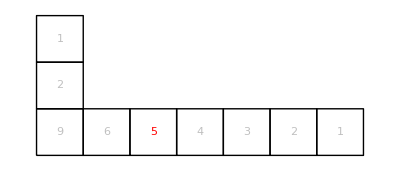
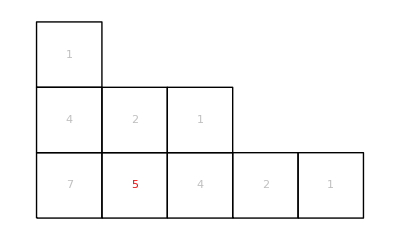
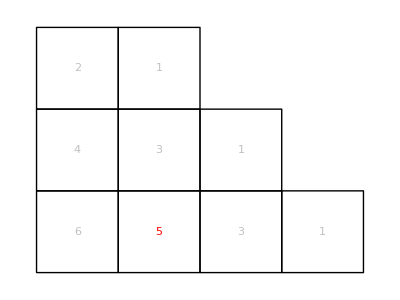
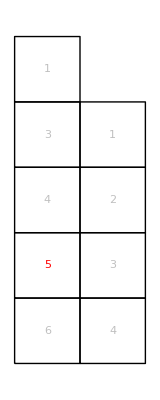
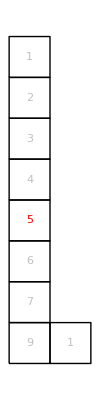

```mathematica
ModHookFerrers[#,5]&/@AddRimHook[{2,1,1},5]
```

```mathematica
AddRimHook[#,5]&/@AddRimHook[{2,1,1},5]
```

{{{12,1,1},{7,6,1},{7,5,2},{7,3,2,2},{7,2,2,2,1},{7,1,1,1,1,1,1,1}},{{10,3,1},{7,6,1},{5,5,4},{5,3,3,2,1},{5,3,2,2,1,1},{5,3,1,1,1,1,1,1}},{{9,3,2},{7,5,2},{5,5,4},{4,3,3,3,1},{4,3,2,2,1,1,1},{4,3,2,1,1,1,1,1}},{{7,2,2,2,1},{6,3,2,2,1},{5,3,3,2,1},{4,3,3,3,1},{2,2,2,2,2,2,1,1},{2,2,2,2,1,1,1,1,1,1}},{{7,1,1,1,1,1,1,1},{5,3,1,1,1,1,1,1},{4,3,2,1,1,1,1,1},{3,3,2,2,1,1,1,1},{2,2,2,2,2,2,1,1},{2,1,1,1,1,1,1,1,1,1,1,1,1}}}

```mathematica
Flatten[AddRimHook[#,5]&/@AddRimHook[{2,1,1},5],1]//CountDistinct
```

{{12,1,1},{7,6,1},{7,5,2},{7,3,2,2},{7,2,2,2,1},{7,1,1,1,1,1,1,1},{10,3,1},{7,6,1},{5,5,4},{5,3,3,2,1},{5,3,2,2,1,1},{5,3,1,1,1,1,1,1},{9,3,2},{7,5,2},{5,5,4},{4,3,3,3,1},{4,3,2,2,1,1,1},{4,3,2,1,1,1,1,1},{7,2,2,2,1},{6,3,2,2,1},{5,3,3,2,1},{4,3,3,3,1},{2,2,2,2,2,2,1,1},{2,2,2,2,1,1,1,1,1,1},{7,1,1,1,1,1,1,1},{5,3,1,1,1,1,1,1},{4,3,2,1,1,1,1,1},{3,3,2,2,1,1,1,1},{2,2,2,2,2,2,1,1},{2,1,1,1,1,1,1,1,1,1,1,1,1}}

```mathematica
Flatten[AddRimHook[#,5]&/@AddRimHook[#,5]&/@AddRimHook[{2,1,1},5],2]//CountDistinct
```

65

```mathematica
Flatten[AddRimHook[#,5]&/@AddRimHook[#,5]&/@AddRimHook[#,5]&/@AddRimHook[{2,1,1},5],3]//CountDistinct
```

190

```mathematica
AddRimHook[{2,1,1},25]
```

{{27,1,1},{25,3,1},{24,3,2},{22,3,2,2},{21,3,2,2,1},{20,3,2,2,1,1},{19,3,2,2,1,1,1},{18,3,2,2,1,1,1,1},{17,3,2,2,1,1,1,1,1},{16,3,2,2,1,1,1,1,1,1},{15,3,2,2,1,1,1,1,1,1,1},{14,3,2,2,1,1,1,1,1,1,1,1},{13,3,2,2,1,1,1,1,1,1,1,1,1},{12,3,2,2,1,1,1,1,1,1,1,1,1,1},{11,3,2,2,1,1,1,1,1,1,1,1,1,1,1},{10,3,2,2,1,1,1,1,1,1,1,1,1,1,1,1},{9,3,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1},{8,3,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{7,3,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{6,3,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{5,3,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{4,3,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{3,3,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{2,2,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}}

```mathematica
Intersection[AddAllRimHooks[{1, 1}, 23, 3], AddAllRimHooks[{2}, 23, 3]]
```

{}

```mathematica
Intersection[{{1, 2, 3}, {2, 4, 1}}, {{1, 2, 3}, {1, 3, 1}}]
```

{{1,2,3}}

```mathematica
AddAllRimHooks[{1, 1, 1}, 33, 5] // Length
```

125

```mathematica
AddAllRimHooks[{2, 1}, 33, 5]//Length
```

125

```mathematica
AddAllRimHooks[{3}, 33, 5]//Length
```

125

```mathematica
p=5;n = 33;
Select[IntegerPartitions@n,Mod[DegreeOfRep@#,p]!=0&] // Length
```

375

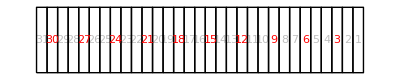
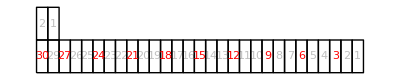
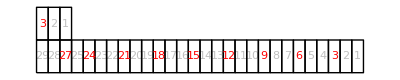
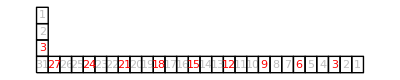
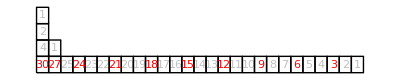
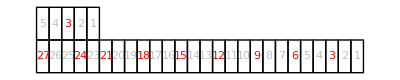
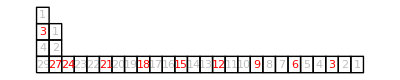
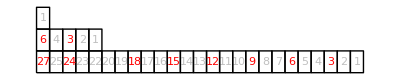
({31} | -Graphics- | {1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0} | (0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)
{29,2} | -Graphics- | {1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0} | (0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)
{28,3} | -Graphics- | {1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0} | (1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0)
{28,1,1,1} | -Graphics- | {1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,0} | (0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0)
{27,2,1,1} | -Graphics- | {1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,1,0} | (0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)
{26,5} | -Graphics- | {1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0} | (0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)
{26,2,2,1} | -Graphics- | {1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,1,0} | (1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0)
{25,5,1} | -Graphics- | {1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,0} | (0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0)
{25,3,3} | -Graphics- | {1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0} | (0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0)
{25,2,2,2} | -Graphics- | {1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,0,0} | (0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0)
{24,5,1,1} | -Graphics- | {1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,1,0} | (0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)
{24,3,3,1} | -Graphics- | {1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,1,0} | (0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)
{23,5,1,1,1} | -Graphics- | {1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,1,1,0} | (0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0)
{23,3,3,1,1} | -Graphics- | {1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,1,1,0} | (0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0)
{23,2,2,2,2} | -Graphics- | {1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,0,0} | (0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0)
{22,5,1,1,1,1} | -Graphics- | {1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,1,1,1,0} | (0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1
1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0)
{22,3,3,1,1,1} | -Graphics- | {1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,1,1,1,0} | (0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1
1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0)
{22,2,2,2,2,1} | -Graphics- | {1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,0,1,0} | (0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1
1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0)
{21,5,1,1,1,1,1} | -Graphics- | {1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,1,1,1,1,0} | (0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 1
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0)
{21,3,3,1,1,1,1} | -Graphics- | {1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,1,1,1,1,0} | (0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0)
{21,2,2,2,2,1,1} | -Graphics- | {1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,0,1,1,0} | (0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1
1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0)
{20,5,1,1,1,1,1,1} | -Graphics- | {1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,1,1,1,1,1,0} | (0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1
1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0)
{20,3,3,1,1,1,1,1} | -Graphics- | {1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,1,1,1,1,1,0} | (0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1
1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0)
{20,2,2,2,2,1,1,1} | -Graphics- | {1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,0,1,1,1,0} | (0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1
1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0)
{19,5,1,1,1,1,1,1,1} | -Graphics- | {1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,1,1,1,1,1,1,0} | (0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1
1 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 0)
{19,3,3,1,1,1,1,1,1} | -Graphics- | {1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,1,1,1,1,1,1,0} | (0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 1
1 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0)
{19,2,2,2,2,1,1,1,1} | -Graphics- | {1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,0,1,1,1,1,0} | (0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1
1 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0)
{18,5,1,1,1,1,1,1,1,1} | -Graphics- | {1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,1,1,1,1,1,1,1,0} | (0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1
0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 1
1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0)
{18,3,3,1,1,1,1,1,1,1} | -Graphics- | {1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,1,1,1,1,1,1,1,0} | (0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1
1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0)
{18,2,2,2,2,1,1,1,1,1} | -Graphics- | {1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,0,1,1,1,1,1,0} | (0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1
1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0)
{17,5,1,1,1,1,1,1,1,1,1} | -Graphics- | {1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,1,1,1,1,1,1,1,1,0} | (0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1
1 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0)
{17,3,3,1,1,1,1,1,1,1,1} | -Graphics- | {1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,1,1,1,1,1,1,1,1,0} | (0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1
1 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 0)
{17,2,2,2,2,1,1,1,1,1,1} | -Graphics- | {1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,0,1,1,1,1,1,1,0} | (0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 1
1 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0)
{16,5,1,1,1,1,1,1,1,1,1,1} | -Graphics- | {1,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,1,1,1,1,1,1,1,1,1,0} | (0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1
1 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 0)
{16,3,3,1,1,1,1,1,1,1,1,1} | -Graphics- | {1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,1,1,1,1,1,1,1,1,1,0} | (0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1
0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 1
1 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 0)
{16,2,2,2,2,1,1,1,1,1,1,1} | -Graphics- | {1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,0,1,1,1,1,1,1,1,0} | (0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1
1 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 0)
{15,5,1,1,1,1,1,1,1,1,1,1,1} | -Graphics- | {1,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,0} | (0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1
0 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 1
1 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0)
{15,3,3,1,1,1,1,1,1,1,1,1,1} | -Graphics- | {1,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,1,1,1,1,1,1,1,1,1,1,0} | (0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 1
0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1
1 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0)
{15,2,2,2,2,1,1,1,1,1,1,1,1} | -Graphics- | {1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,0,1,1,1,1,1,1,1,1,0} | (0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1
0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1
1 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 0)
{14,5,1,1,1,1,1,1,1,1,1,1,1,1} | -Graphics- | {1,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,0} | (0 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1
1 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 0)
{14,3,3,1,1,1,1,1,1,1,1,1,1,1} | -Graphics- | {1,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,1,1,1,1,1,1,1,1,1,1,1,0} | (0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1
1 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 0)
{14,2,2,2,2,1,1,1,1,1,1,1,1,1} | -Graphics- | {1,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,0,1,1,1,1,1,1,1,1,1,0} | (0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1
0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 1
1 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 0)
{13,5,1,1,1,1,1,1,1,1,1,1,1,1,1} | -Graphics- | {1,0,0,0,0,0,0,0,0,1,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,0} | (0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1
0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1
1 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 1 | 0)
{13,3,3,1,1,1,1,1,1,1,1,1,1,1,1} | -Graphics- | {1,0,0,0,0,0,0,0,0,0,0,1,1,0,0,1,1,1,1,1,1,1,1,1,1,1,1,0} | (0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1
0 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 1
1 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 0)
{13,2,2,2,2,1,1,1,1,1,1,1,1,1,1} | -Graphics- | {1,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,0} | (0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 1
0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1
1 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 0)
{12,5,1,1,1,1,1,1,1,1,1,1,1,1,1,1} | -Graphics- | {1,0,0,0,0,0,0,0,1,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0} | (0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1
0 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 1 | 1
1 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 0)
{12,3,3,1,1,1,1,1,1,1,1,1,1,1,1,1} | -Graphics- | {1,0,0,0,0,0,0,0,0,0,1,1,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,0} | (0 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 1
0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1
1 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 0)
{12,2,2,2,2,1,1,1,1,1,1,1,1,1,1,1} | -Graphics- | {1,0,0,0,0,0,0,0,0,0,0,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,0} | (0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1
0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1
1 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 0)
{11,5,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1} | -Graphics- | {1,0,0,0,0,0,0,1,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0} | (0 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 1 | 1
0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1
1 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 0)
{11,3,3,1,1,1,1,1,1,1,1,1,1,1,1,1,1} | -Graphics- | {1,0,0,0,0,0,0,0,0,1,1,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0} | (0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1
0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1
1 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 1 | 0)
{11,2,2,2,2,1,1,1,1,1,1,1,1,1,1,1,1} | -Graphics- | {1,0,0,0,0,0,0,0,0,0,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,0} | (0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1
0 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 1
1 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 0)
{10,5,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1} | -Graphics- | {1,0,0,0,0,0,1,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0} | (0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1
0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1
1 | 0 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 0)
{10,3,3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1} | -Graphics- | {1,0,0,0,0,0,0,0,1,1,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0} | (0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1
0 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 1 | 1
1 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 0)
{10,2,2,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1} | -Graphics- | {1,0,0,0,0,0,0,0,0,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,0} | (0 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 1
0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1
1 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 0)
{9,5,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1} | -Graphics- | {1,0,0,0,0,1,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0} | (0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1
0 | 0 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1
1 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 0)
{9,3,3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1} | -Graphics- | {1,0,0,0,0,0,0,1,1,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0} | (0 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 1 | 1
0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 0)
{9,2,2,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1} | -Graphics- | {1,0,0,0,0,0,0,0,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0} | (0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1
0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 1 | 0)
{8,5,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1} | -Graphics- | {1,0,0,0,1,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0} | (0 | 0 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1
0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1
1 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 0)
{8,3,3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1} | -Graphics- | {1,0,0,0,0,0,1,1,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0} | (0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1
0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1
1 | 0 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 0)
{8,2,2,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1} | -Graphics- | {1,0,0,0,0,0,0,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0} | (0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1
0 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 1 | 1
1 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 0)
{7,5,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1} | -Graphics- | {1,0,0,1,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0} | (0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1
0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 0)
{7,3,3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1} | -Graphics- | {1,0,0,0,0,1,1,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0} | (0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1
0 | 0 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1
1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0)
{7,2,2,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1} | -Graphics- | {1,0,0,0,0,0,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0} | (0 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 1 | 1
0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0)
{6,5,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1} | -Graphics- | {1,0,1,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0} | (0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1
0 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 0)
{6,3,3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1} | -Graphics- | {1,0,0,0,1,1,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0} | (0 | 0 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1
0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 0)
{6,2,2,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1} | -Graphics- | {1,0,0,0,0,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0} | (0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1
0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 0 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 0)
{5,5,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1} | -Graphics- | {1,1,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0} | (0 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1
0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0)
{5,3,3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1} | -Graphics- | {1,0,0,1,1,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0} | (0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 0)
{5,2,2,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1} | -Graphics- | {1,0,0,0,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0} | (0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
0 | 0 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1
1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0)
{4,4,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1} | -Graphics- | {1,1,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0} | (0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0)
{4,3,3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1} | -Graphics- | {1,0,1,1,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0} | (0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1
0 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0)
{4,3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1} | -Graphics- | {1,0,1,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0} | (1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0)
{4,2,2,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1} | -Graphics- | {1,0,0,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0} | (0 | 0 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1
0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0)
{4,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1} | -Graphics- | {1,0,0,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0} | (0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0)
{4,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1} | -Graphics- | {1,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0} | (0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0)
{3,3,3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1} | -Graphics- | {1,1,1,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0} | (0 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1
0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0)
{3,2,2,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1} | -Graphics- | {1,0,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0} | (0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 0)
{2,2,2,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1} | -Graphics- | {1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0} | (0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
0 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0)
{2,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1} | -Graphics- | {1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0} | (1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0)
{2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1} | -Graphics- | {1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0} | (0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0)
{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1} | -Graphics- | {1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0} | (0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0))

```mathematica
p=3;n = 31;
({#,ModHookFerrers[#,p],PartitionToAbaci@#,MatrixForm@AbaciRunners[PartitionToAbaci@#,p]}&/@Select[IntegerPartitions@n,Mod[DegreeOfRep@#,p]!=0&])//MatrixForm
```

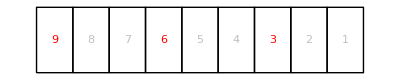
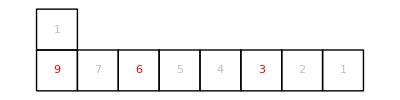
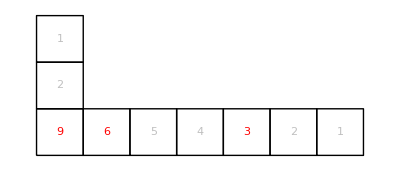
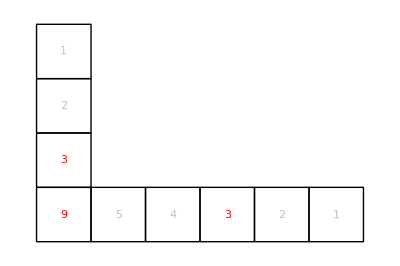
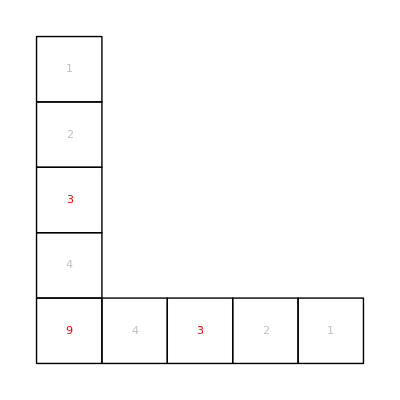
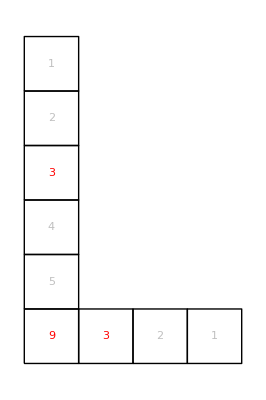
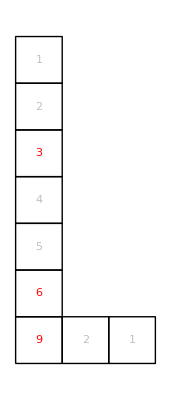
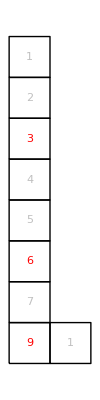
({9} | -Graphics- | {1,0,0,0,0,0,0,0,0,0} | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
1 | 0 | 0 | 0)
{8,1} | -Graphics- | {1,0,0,0,0,0,0,0,1,0} | (0 | 0 | 0 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0)
{7,1,1} | -Graphics- | {1,0,0,0,0,0,0,1,1,0} | (0 | 0 | 0 | 1
0 | 0 | 0 | 1
1 | 0 | 0 | 0)
{6,1,1,1} | -Graphics- | {1,0,0,0,0,0,1,1,1,0} | (0 | 0 | 0 | 1
0 | 0 | 0 | 1
1 | 0 | 1 | 0)
{5,1,1,1,1} | -Graphics- | {1,0,0,0,0,1,1,1,1,0} | (0 | 0 | 0 | 1
0 | 0 | 1 | 1
1 | 0 | 1 | 0)
{4,1,1,1,1,1} | -Graphics- | {1,0,0,0,1,1,1,1,1,0} | (0 | 0 | 1 | 1
0 | 0 | 1 | 1
1 | 0 | 1 | 0)
{3,1,1,1,1,1,1} | -Graphics- | {1,0,0,1,1,1,1,1,1,0} | (0 | 0 | 1 | 1
0 | 0 | 1 | 1
1 | 1 | 1 | 0)
{2,1,1,1,1,1,1,1} | -Graphics- | {1,0,1,1,1,1,1,1,1,0} | (0 | 0 | 1 | 1
0 | 1 | 1 | 1
1 | 1 | 1 | 0)
{1,1,1,1,1,1,1,1,1} | -Graphics- | {1,1,1,1,1,1,1,1,1,0} | (0 | 1 | 1 | 1
0 | 1 | 1 | 1
1 | 1 | 1 | 0))

```mathematica
p=3;
({#,ModHookFerrers[#,p],PartitionToAbaci@#,MatrixForm@AbaciRunners[PartitionToAbaci@#,p]}&/@Select[IntegerPartitions@9,Mod[DegreeOfRep@#,p]!=0&&Core[#,p]=={}&])//MatrixForm
```

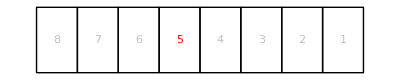
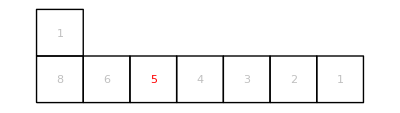
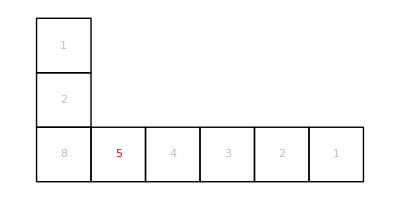
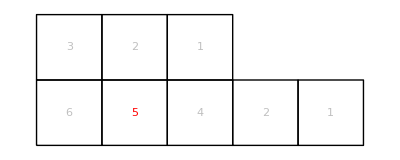
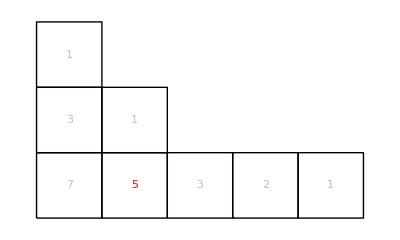
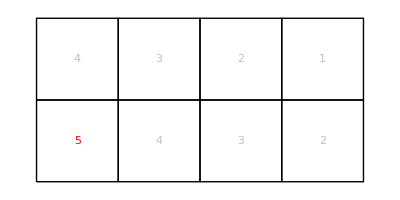
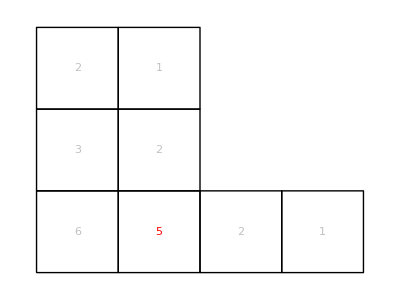
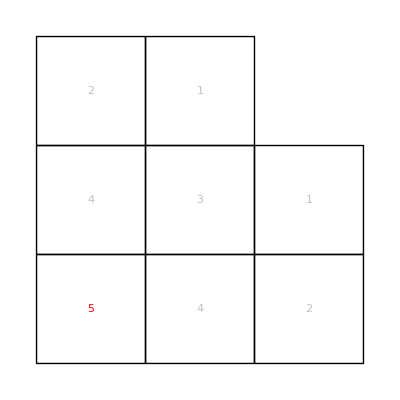
({8} | -Graphics- | {1,0,0,0,0,0,0,0,0} | (0 | 0
1 | 0
0 | 0
0 | 0
0 | 0)
{7,1} | -Graphics- | {1,0,0,0,0,0,0,1,0} | (0 | 0
1 | 0
0 | 0
0 | 1
0 | 0)
{6,1,1} | -Graphics- | {1,0,0,0,0,0,1,1,0} | (0 | 0
1 | 0
0 | 1
0 | 1
0 | 0)
{5,3} | -Graphics- | {1,0,0,1,0,0,0} | (0 | 0
0 | 1
0 | 0
1 | 0
0 | 0)
{5,2,1} | -Graphics- | {1,0,0,0,1,0,1,0} | (0 | 0
0 | 1
1 | 0
0 | 1
0 | 0)
{4,4} | -Graphics- | {1,1,0,0,0,0} | (0 | 1
0 | 0
0 | 0
0 | 0
1 | 0)
{4,2,2} | -Graphics- | {1,0,0,1,1,0,0} | (0 | 0
0 | 1
0 | 1
1 | 0
0 | 0)
{3,3,2} | -Graphics- | {1,1,0,1,0,0} | (0 | 1
0 | 0
0 | 1
0 | 0
1 | 0)
{3,3,1,1} | -Graphics- | {1,1,0,0,1,1,0} | (0 | 0
0 | 0
0 | 1
1 | 1
1 | 0)
{3,2,1,1,1} | -Graphics- | {1,0,1,0,1,1,1,0} | (0 | 0
0 | 1
1 | 1
0 | 1
1 | 0)
{3,1,1,1,1,1} | -Graphics- | {1,0,0,1,1,1,1,1,0} | (0 | 1
1 | 1
0 | 1
0 | 1
1 | 0)
{2,2,2,2} | -Graphics- | {1,1,1,1,0,0} | (0 | 1
0 | 1
0 | 1
0 | 0
1 | 0)
{2,2,2,1,1} | -Graphics- | {1,1,1,0,1,1,0} | (0 | 1
0 | 0
0 | 1
1 | 1
1 | 0)
{2,1,1,1,1,1,1} | -Graphics- | {1,0,1,1,1,1,1,1,0} | (0 | 1
1 | 1
0 | 1
1 | 1
1 | 0)
{1,1,1,1,1,1,1,1} | -Graphics- | {1,1,1,1,1,1,1,1,0} | (0 | 1
1 | 1
1 | 1
1 | 1
1 | 0))

```mathematica
p=5;
({#,ModHookFerrers[#,p],PartitionToAbaci@#,MatrixForm@AbaciRunners[PartitionToAbaci@#,p]}&/@Select[IntegerPartitions@8,Mod[DegreeOfRep@#,p]!=0&])//MatrixForm
```

```mathematica
Core[λ_,p_]:=Cases[AbaciToPartition@Flatten@Transpose[AbaciRunners[PartitionToAbaci@λ,p]//.{{x___,1,y___,0,z___}->{x,0,y,1,z}}],_?Positive]
```

```mathematica
p=13;
(Core[#,p]&/@Select[IntegerPartitions@25,Mod[DegreeOfRep@#,p]!=0&])//Tally
```

{{{12},13},{{11,1},13},{{10,2},13},{{10,1,1},13},{{9,3},13},{{9,2,1},13},{{9,1,1,1},13},{{8,4},13},{{8,3,1},13},{{8,2,2},13},{{8,2,1,1},13},{{8,1,1,1,1},13},{{7,5},13},{{7,4,1},13},{{7,3,2},13},{{7,3,1,1},13},{{7,2,2,1},13},{{7,2,1,1,1},13},{{7,1,1,1,1,1},13},{{6,6},13},{{6,5,1},13},{{6,4,2},13},{{6,4,1,1},13},{{6,3,3},13},{{6,3,2,1},13},{{6,3,1,1,1},13},{{6,2,2,2},13},{{6,2,2,1,1},13},{{6,2,1,1,1,1},13},{{6,1,1,1,1,1,1},13},{{5,5,2},13},{{5,5,1,1},13},{{5,4,3},13},{{5,4,2,1},13},{{5,4,1,1,1},13},{{5,3,3,1},13},{{5,3,2,2},13},{{5,3,2,1,1},13},{{5,3,1,1,1,1},13},{{5,2,2,2,1},13},{{5,2,2,1,1,1},13},{{5,2,1,1,1,1,1},13},{{5,1,1,1,1,1,1,1},13},{{4,4,4},13},{{4,4,3,1},13},{{4,4,2,2},13},{{4,4,2,1,1},13},{{4,4,1,1,1,1},13},{{4,3,3,2},13},{{4,3,3,1,1},13},{{4,3,2,2,1},13},{{4,3,2,1,1,1},13},{{4,3,1,1,1,1,1},13},{{4,2,2,2,2},13},{{4,2,2,2,1,1},13},{{4,2,2,1,1,1,1},13},{{4,2,1,1,1,1,1,1},13},{{4,1,1,1,1,1,1,1,1},13},{{3,3,3,3},13},{{3,3,3,2,1},13},{{3,3,3,1,1,1},13},{{3,3,2,2,2},13},{{3,3,2,2,1,1},13},{{3,3,2,1,1,1,1},13},{{3,3,1,1,1,1,1,1},13},{{3,2,2,2,2,1},13},{{3,2,2,2,1,1,1},13},{{3,2,2,1,1,1,1,1},13},{{3,2,1,1,1,1,1,1,1},13},{{3,1,1,1,1,1,1,1,1,1},13},{{2,2,2,2,2,2},13},{{2,2,2,2,2,1,1},13},{{2,2,2,2,1,1,1,1},13},{{2,2,2,1,1,1,1,1,1},13},{{2,2,1,1,1,1,1,1,1,1},13},{{2,1,1,1,1,1,1,1,1,1,1},13},{{1,1,1,1,1,1,1,1,1,1,1,1},13}}